```mathematica
A=-2.099750428405166

P= Exp[0.16*A]*0.6*75.20+Exp[0.36A]*0.4*31.66
```

-2.09975

38.1919

```mathematica
x1=0.294
x2=1-x1
Solve[B*x2^2-B*x1^2== Log[31.66/75.20],B]
```

0.294

0.706

{{B→-2.09975}}

```mathematica
∫_8^30 (2000*Log[140000/(140000-2100*t)]-9.8t)ⅆt
```

11061.3

```mathematica
f[t_]:= (2000*Log[140000/(140000-2100*t)]-9.8t)

f[30]
```

901.674

```mathematica
g[n_]:=(30-8)/(2*n)*(f[8]+2*∑_(i=1)^(n-1) (2000*Log[140000/(140000-2100*(8+i*(30-8)/n))]-9.8*(8+i*(30-8)/n))+f[30])
```

```mathematica
g[64]
```

11061.5

```mathematica
j[θ_]:= -2.2067*10^-12*(θ^4-81*10^8)

1200+j[1200]*60
```

926.524

```mathematica
926.524+j[926.524]*60
```

830.025

```mathematica
830.025+j[830.025]*60
```

768.254

```mathematica
768.254+j[768.254]*60
```

723.204

```mathematica
723.204+j[723.204]*60
```

688.057

```mathematica
688.057+j[688.057]*60
```

659.454

```mathematica
659.454+j[659.454]*60
```

635.487

```mathematica
635.487+j[635.487]*60
```

614.966

```mathematica
Clear[x1,x2,A,B]
x2=1-x1
eqn1=x1*x2*(A+B(x1-x2))

eqn2=Expand[eqn1]
```

1-x1

(1-x1) x1 (A+B (-1+2 x1))

A x1-B x1-A x1^2+3 B x1^2-2 B x1^3

```mathematica
D[eqn2,{x1,2}]
```

-2 A+6 B-12 B x1

```mathematica
A=1.8795
B=0.6855
Solve[1/(x1*x2)+(-2 A+6 B-12 B x1)== 0,x1]
```

1.8795

0.6855

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x1→-0.286619},{x1→0.531198},{x1→0.798455}}

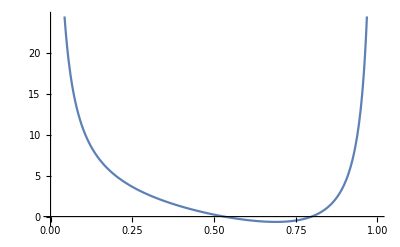

```mathematica
Plot[1/(x1*x2)+(-2 A+6 B-12 B x1)== 0,{x1,0,1}]
```

```mathematica
x1α=0.0959
x1β=0.9924
X= x1α/(1-x1α)
Y=x1β/(1-x1β)
Θ= Log[x1β/x1α]
Λ=Log[(1-x1β)/(1-x1α)]
A=-((X-Y)(X*Θ+Λ)^2(Y*Θ+Λ)^2)/((Θ*(X+Y)+2*Λ)(Y*Λ+X*(2*Y*Θ+Λ))^2)
B=((X-Y)(X*Θ+Λ)^2(Y*Θ+Λ)^2)/((Θ*(X+Y)+2*Λ)^2(Y*Λ+X*(2*Y*Θ+Λ)))
```

0.0959

0.9924

0.106072

130.579

2.33682

-4.77879

2.60674

4.9326

```mathematica
Clear[A,B,x1,x2]
```

```mathematica
x2=1-x1
y= x2^2*(A+3*B-4*B*x2)
Expand[y]
Clear[x1α,x1β]
```

1-x1

(A+3 B-4 B (1-x1)) (1-x1)^2

A-B-2 A x1+6 B x1+A x1^2-9 B x1^2+4 B x1^3

```mathematica
(A-B-2 *A *x1α+6*B*x1α+A x1α^2-9 B *x1α^2+4 B *x1α^3)-(A-B-2 *A *x1β+6*B*x1β+A x1β^2-9 B *x1β^2+4 B* x1β^3)== Log[x1α/x1β]
(x1α^2*(A-3*B+4*B*x1α))-(x1β^2*(A-3*B+4*B*x1β))== Log[(1-x1α)/(1-x1β)]
NSolve[{(A-B-2 *A *x1α+6*B*x1α+A x1α^2-9 B *x1α^2+4 B *x1α^3)-(A-B-2 *A *x1β+6*B*x1β+A x1β^2-9 B *x1β^2+4 B* x1β^3)== Log[x1α/x1β],(x1α^2*(A-3*B+4*B*x1α))-(x1β^2*(A-3*B+4*B*x1β))== Log[(1-x1α)/(1-x1β)]},{x1α,x1β},Reals]
```

-2 A x1α+6 B x1α+A x1α^2-9 B x1α^2+4 B x1α^3+2 A x1β-6 B x1β-A x1β^2+9 B x1β^2-4 B x1β^3==Log[x1α/x1β]

x1α^2 (A-3 B+4 B x1α)-x1β^2 (A-3 B+4 B x1β)==Log[(1-x1α)/(1-x1β)]